```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
mup[k_]=Sqrt[(k+1)*(Np-k)];
mdown[k_]=Sqrt[k*(Np-k+1)];
eqn[k1_,k2_]=psi[k1,k2]'[t]==-I*(mup[k1]*mup[k2]*psi[k1+1,k2+1][t]+mdown[k1]*mdown[k2]*psi[k1-1,k2-1][t])+0.1;
pinitial[k1_,k2_]=If[(k1==Np)&&(k2==Np),1.0,0.0];
rho[t_]:=ArrayFlatten[Table[Sum[psol[k1, k2][t]*Conjugate[psol[k1p, k2][t]], {k2, 0, Np}], {k1, 0, Np},{k1p, 0, Np}]];
lamb[t_]:=Eigenvalues[rho[t]];
entanglement[t_]:=If[t==0,0,-(lamb[t].Log[Np+1,lamb[t]])];
```

```mathematica
Np=5; tmax=2.0*Pi;
vars={};
equations={};
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations=Append[equations,eqn[k1,k2]];
];
];
For[k1=0,k1≤Np,k1=k1+1,
For[k2=0,k2≤Np,k2=k2+1,
equations=Append[equations,psi[k1,k2][0]==pinitial[k1,k2]];
vars=Append[vars,psi[k1,k2]];
];
];
solutions=NDSolve[equations,vars,{t,0,tmax}];
Clear[k1,k2];
psoltemp[k1_,k2_]:=psi[k1,k2]/.solutions[[1]][[k1*(Np+1)+k2+1]];
psol[k1_,k2_]:=Function[τ,psoltemp[k1,k2][τ]];

rho[5.8]//MatrixForm
```

```mathematica
p1=Plot[{entanglement[t]},{t,0,tmax},Frame->True,PlotRange->{-0.000001,1},FrameLabel->{"t","E_S/E_max"},
FrameTicks->{{Automatic, None},{{0, Pi/2, Pi, 3Pi/2, 2Pi},Automatic}}]
```

```mathematica
taumax=2*Pi;
nopoints=20*Np;
datalist=Table[{τ,entanglement[τ]},{τ,0.0,taumax,taumax/nopoints}];
```

```mathematica
datalist10={{0.,0},{0.031415926535897934,0.1403411221536703},{0.06283185307179587,0.3606127547305631},{0.0942477796076938,0.5774970560192785},{0.12566370614359174,0.7597979297439116},{0.15707963267948966,0.8866426150438405},{0.1884955592153876,0.9432460898100978},{0.21991148575128555,0.9234216812057525},{0.25132741228718347,0.8324262405516414},{0.2827433388230814,0.6912856806908025},{0.3141592653589793,0.537778118183399},{0.3455751918948773,0.37807395649771375},{0.3769911184307752,0.23560416941670223},{0.4084070449666731,0.22113382930398973},{0.4398229715025711,0.35252498756293454},{0.471238898038469,0.5289701484214436},{0.5026548245743669,0.7041266735292208},{0.5340707511102649,0.856428236771418},{0.5654866776461628,0.9203318947948439},{0.5969026041820608,0.9364024481142463},{0.6283185307179586,0.8669513446703384},{0.6597344572538566,0.7986996309090671},{0.6911503837897546,0.7324268458765688},{0.7225663103256524,0.6570659333730293},{0.7539822368615504,0.5444370454482356},{0.7853981633974484,0.46852663490712665},{0.8168140899333463,0.42013771456392385},{0.8482300164692442,0.3987138083710168},{0.8796459430051422,0.5324696822414161},{0.9110618695410401,0.7075378782805916},{0.942477796076938,0.7763526363608998},{0.9738937226128359,0.8687687441157511},{1.0053096491487339,0.8759984516420993},{1.0367255756846319,0.8109271637835954},{1.0681415022205298,0.8133032077322419},{1.0995574287564276,0.801552298981428},{1.1309733552923256,0.7397814796036511},{1.1623892818282235,0.734914633763393},{1.1938052083641215,0.627937032663158},{1.2252211349000195,0.43383330959718563},{1.2566370614359172,0.4119290527304108},{1.2880529879718152,0.5721846930721152},{1.3194689145077132,0.6861423450132483},{1.3508848410436112,0.72899147387269},{1.3823007675795091,0.7691493291904506},{1.4137166941154071,0.798484983503958},{1.4451326206513049,0.8194417193791366},{1.4765485471872029,0.7845712973335739},{1.5079644737231008,0.7520164266624452},{1.5393804002589988,0.7894481793406798},{1.5707963267948968,0.7273497297487219},{1.6022122533307945,0.5739676024851753},{1.6336281798666925,0.4803146165267022},{1.6650441064025905,0.6053215916841265},{1.6964600329384885,0.7380809443092078},{1.7278759594743864,0.7257247989773712},{1.7592918860102844,0.6285521994421157},{1.7907078125461822,0.7143820133185153},{1.8221237390820801,0.8123405856077308},{1.8535396656179781,0.7609918723358388},{1.884955592153876,0.6251768797400401},{1.916371518689774,0.627436053544508},{1.9477874452256718,0.710619120438657},{1.9792033717615698,0.7660828305758021},{2.0106192982974678,0.7135482668180142},{2.0420352248333655,0.677292099218988},{2.0734511513692637,0.7462401761484745},{2.1048670779051615,0.7655968883453229},{2.1362830044410597,0.6942840447129034},{2.1676989309769574,0.7049866201313806},{2.199114857512855,0.7440652097660065},{2.2305307840487534,0.6988483668209691},{2.261946710584651,0.5471547858484366},{2.2933626371205493,0.49253179647800527},{2.324778563656447,0.6523760142440466},{2.356194490192345,0.7939400187812174},{2.387610416728243,0.7778455987394558},{2.419026343264141,0.7644390518651631},{2.450442269800039,0.7867184805398733},{2.4818581963359367,0.7424325563270547},{2.5132741228718345,0.7933706458711598},{2.5446900494077327,0.8256957610305393},{2.5761059759436304,0.7442939719122224},{2.6075219024795286,0.7251802056744042},{2.6389378290154264,0.6243291433594073},{2.6703537555513246,0.4585208049006357},{2.7017696820872223,0.510893241611959},{2.73318560862312,0.5960423992191084},{2.7646015351590183,0.629617135691754},{2.796017461694916,0.7127949315070551},{2.8274333882308142,0.7452764672678232},{2.858849314766712,0.7571934149160469},{2.8902652413026098,0.7929947731132891},{2.921681167838508,0.8897887098252504},{2.9530970943744057,0.9079109019803403},{2.984513020910304,0.8468689909121568},{3.0159289474462017,0.7498498636716593},{3.0473448739820994,0.5992491679348204},{3.0787608005179976,0.47941090248085066},{3.1101767270538954,0.36707412364194103},{3.1415926535897936,0.3535900393524575},{3.1730085801256913,0.4599237170692471},{3.204424506661589,0.5732395592949101},{3.2358404331974873,0.6669746686804039},{3.267256359733385,0.7792281423221251},{3.298672286269283,0.8833443806558721},{3.330088212805181,0.9395185686585402},{3.3615041393410787,0.9136070866845146},{3.392920065876977,0.8068255989457391},{3.4243359924128747,0.6550651811320076},{3.455751918948773,0.4708039453956324},{3.4871678454846706,0.26651993625960296},{3.518583772020569,0.09363993263408607},{3.5499996985564666,0.15258202965663575},{3.5814156250923643,0.3484141389601558},{3.6128315516282625,0.5490668715549405},{3.6442474781641603,0.7252708790779425},{3.6756634047000585,0.8605790075687151},{3.7070793312359562,0.9342545571725293},{3.738495257771854,0.9339677852963774},{3.769911184307752,0.8643136609910114},{3.80132711084365,0.7368894345777577},{3.832743037379548,0.5663420163420894},{3.864158963915446,0.38283502927217417},{3.8955748904513436,0.20244692488718294},{3.926990816987242,0.13658275551743068},{3.9584067435231396,0.2643435662021201},{3.989822670059038,0.4546578150189291},{4.0212385965949355,0.6557007972969322},{4.052654523130833,0.8104133960455866},{4.084070449666731,0.8941344157850806},{4.11548637620263,0.9312564401043281},{4.1469023027385274,0.911722157296153},{4.178318229274425,0.8420038922025226},{4.209734155810323,0.7473766300478193},{4.241150082346221,0.6293459683246498},{4.272566008882119,0.5067745892688981},{4.303981935418017,0.3771800317029166},{4.335397861953915,0.29836308700607644},{4.366813788489813,0.3371834241149828},{4.39822971502571,0.465680699916686},{4.429645641561609,0.6557744844716333},{4.461061568097507,0.7782774011882627},{4.4924774946334045,0.8737369359724222},{4.523893421169302,0.9087973338234971},{4.5553093477052,0.8756123487899612},{4.586725274241099,0.8411441720206112},{4.618141200776996,0.8163538357309537},{4.649557127312894,0.7288530273347503},{4.680973053848792,0.6522411726179626},{4.71238898038469,0.558510127578424},{4.743804906920588,0.38453217340795065},{4.775220833456486,0.3055011617826989},{4.806636759992384,0.4571727426011486},{4.838052686528282,0.6138172815030654},{4.869468613064179,0.7191796214714093},{4.900884539600078,0.8221023735380372},{4.932300466135976,0.8508229518292955},{4.9637163926718735,0.8595376296421785},{4.995132319207771,0.8573341013777498},{5.026548245743669,0.7973944684364678},{5.057964172279568,0.7708434611339859},{5.089380098815465,0.7134185816006927},{5.120796025351363,0.5383005169499052},{5.152211951887261,0.3578429169129207},{5.1836278784231595,0.4078124358244022},{5.215043804959057,0.5961008488617003},{5.246459731494955,0.6943242826283177},{5.277875658030853,0.6848829349984034},{5.3092915845667505,0.7461568603516344},{5.340707511102649,0.8387827951245078},{5.372123437638547,0.84989248194305},{5.403539364174445,0.7581324019683449},{5.4349552907103424,0.6960014777972999},{5.46637121724624,0.696618781219393},{5.497787143782139,0.7013265509080819},{5.529203070318037,0.6453466195773593},{5.560618996853934,0.5563868729587179},{5.592034923389832,0.6186151433256734},{5.62345084992573,0.7104532349884786},{5.6548667764616285,0.6747692089167328},{5.686282702997526,0.6772485218099997},{5.717698629533424,0.7619485383180181},{5.749114556069322,0.8083396679148463},{5.7805304826052195,0.6949839492187425},{5.811946409141118,0.5923117763023316},{5.843362335677016,0.6490859494176696},{5.874778262212914,0.7924117901220773},{5.906194188748811,0.7977546608681082},{5.937610115284709,0.7131971700699403},{5.969026041820608,0.7354647442293315},{6.000441968356506,0.6940624714985282},{6.031857894892403,0.6873593513175387},{6.063273821428301,0.7610705057436025},{6.094689747964199,0.7141899180655078},{6.1261056745000975,0.7002200874068147},{6.157521601035995,0.6999910958805363},{6.188937527571893,0.5635122280939381},{6.220353454107791,0.5542204426586121},{6.2517693806436885,0.685259383195238},{6.283185307179587,0.7206618065282924}};
```

```mathematica
datalist20={{0.,0},{0.015707963267948967,0.11107590387057137},{0.031415926535897934,0.28934400153277756},{0.0471238898038469,0.4741207045122125},{0.06283185307179587,0.6453750376764007},{0.07853981633974483,0.7894751336813893},{0.0942477796076938,0.8939244785767431},{0.10995574287564278,0.9484979338100327},{0.12566370614359174,0.9478000702819744},{0.1413716694115407,0.8926503209328347},{0.15707963267948966,0.7901409360530292},{0.17278759594743864,0.65490066909748},{0.1884955592153876,0.5163278258567668},{0.20420352248333656,0.38787289247196216},{0.21991148575128555,0.26616272776733857},{0.2356194490192345,0.19607117851902076},{0.25132741228718347,0.2555991686294301},{0.26703537555513246,0.38374629143364253},{0.2827433388230814,0.5317713474464602},{0.2984513020910304,0.676522690650291},{0.3141592653589793,0.8036285744626865},{0.3298672286269283,0.9082125295551425},{0.3455751918948773,0.9657050703039007},{0.3612831551628262,0.9665542889819698},{0.3769911184307752,0.9168912509144604},{0.3926990816987242,0.8164831486305152},{0.4084070449666731,0.7357096049947155},{0.4241150082346221,0.6676020201538335},{0.4398229715025711,0.6011393900449182},{0.45553093477052004,0.5134930618603776},{0.471238898038469,0.45580672851719806},{0.48694686130641796,0.40181128915179876},{0.5026548245743669,0.41989548424863504},{0.5183627878423159,0.4993382981993224},{0.5340707511102649,0.569799141389608},{0.5497787143782138,0.6756136084106649},{0.5654866776461628,0.8142272903221601},{0.5811946409141118,0.8656534401014162},{0.5969026041820608,0.9126540192130005},{0.6126105674500097,0.9162966685540928},{0.6283185307179586,0.8473899517228473},{0.6440264939859076,0.8050126596786298},{0.6597344572538566,0.7587988323157003},{0.6754424205218056,0.7419359382216343},{0.6911503837897546,0.72053795012938},{0.7068583470577036,0.6251680786916836},{0.7225663103256524,0.575357279229099},{0.7382742735936014,0.5496116280227789},{0.7539822368615504,0.4856495237979816},{0.7696902001294994,0.44456143085792493},{0.7853981633974484,0.5596408673728919},{0.8011061266653973,0.6922150738917934},{0.8168140899333463,0.7485379939674898},{0.8325220532012952,0.7914022029185326},{0.8482300164692442,0.8601403806480061},{0.8639379797371932,0.8576068461856479},{0.8796459430051422,0.7944889174452018},{0.8953539062730911,0.8094072094909025},{0.9110618695410401,0.8423904170986818},{0.9267698328089891,0.7975697189720714},{0.942477796076938,0.7417080389391569},{0.958185759344887,0.7289995883191935},{0.9738937226128359,0.6778099191929658},{0.9896016858807849,0.5423538583005154},{1.0053096491487339,0.4488584882456773},{1.0210176124166828,0.4615749312040108},{1.0367255756846319,0.5720217584364193},{1.0524335389525807,0.6607146330765279},{1.0681415022205298,0.7321144811154773},{1.0838494654884787,0.7780278311373033},{1.0995574287564276,0.7815758105335403},{1.1152653920243767,0.8087128852128529},{1.1309733552923256,0.8761055344494949},{1.1466813185602747,0.8553017162397353},{1.1623892818282235,0.779894663840592},{1.1780972450961724,0.7547368342465646},{1.1938052083641215,0.7882931160631863},{1.2095131716320704,0.7253105078741952},{1.2252211349000195,0.576271217244017},{1.2409290981679684,0.44331470149838914},{1.2566370614359172,0.419047638272417},{1.2723450247038663,0.5826908798841908},{1.2880529879718152,0.7161959545538811},{1.3037609512397643,0.7490956821319825},{1.3194689145077132,0.7448452778205024},{1.3351768777756623,0.7419792589866978},{1.3508848410436112,0.8075590595543076},{1.36659280431156,0.852444359225648},{1.3823007675795091,0.832677910314073},{1.398008730847458,0.7538325618681321},{1.4137166941154071,0.6942123356089496},{1.429424657383356,0.6495161355127017},{1.4451326206513049,0.6451906363559111},{1.460840583919254,0.6056396693045907},{1.4765485471872029,0.5624240551611047},{1.492256510455152,0.581555215180506},{1.5079644737231008,0.6612523709934652},{1.5236724369910497,0.7598361054135454},{1.5393804002589988,0.8109172431702356},{1.5550883635269477,0.7565122125878245},{1.5707963267948968,0.7039297742358824},{1.5865042900628457,0.7542989332589404},{1.6022122533307945,0.8116904397884653},{1.6179202165987436,0.8138789802159624},{1.6336281798666925,0.6921358606405268},{1.6493361431346416,0.5299927496196642},{1.6650441064025905,0.5439859483446585},{1.6807520696705394,0.6332561946634929},{1.6964600329384885,0.7429390156021994},{1.7121679962064373,0.7816407564509933},{1.7278759594743864,0.7119063978476289},{1.7435839227423353,0.7060100695535237},{1.7592918860102844,0.7836547245323637},{1.7749998492782333,0.8286485972382187},{1.7907078125461822,0.7638345168447902},{1.8064157758141313,0.7048339173456128},{1.8221237390820801,0.7452574386766886},{1.8378317023500292,0.755500377606027},{1.8535396656179781,0.7291295433886368},{1.869247628885927,0.6346023081177402},{1.884955592153876,0.5406621791153128},{1.900663555421825,0.5224248887181447},{1.916371518689774,0.6399975798417137},{1.932079481957723,0.7482111906118349},{1.9477874452256718,0.769352550272143},{1.963495408493621,0.728645644885414},{1.9792033717615698,0.7883419182845405},{1.994911335029519,0.8182139758650728},{2.0106192982974678,0.7544829471998332},{2.0263272615654166,0.7423285601870976},{2.0420352248333655,0.8184814387700975},{2.057743188101315,0.8141717766452646},{2.0734511513692637,0.7290287041048931},{2.0891591146372126,0.7287364020067228},{2.1048670779051615,0.708993671371023},{2.1205750411731104,0.5883363223767983},{2.1362830044410597,0.4696741957418337},{2.1519909677090086,0.5692145897601623},{2.1676989309769574,0.6668718196174023},{2.1834068942449063,0.6765192903432833},{2.199114857512855,0.6763597654194273},{2.2148228207808045,0.773534448409525},{2.2305307840487534,0.7768497105441117},{2.2462387473167023,0.7324558496686876},{2.261946710584651,0.7608961287479693},{2.2776546738526,0.8139193905240503},{2.2933626371205493,0.8634081830440725},{2.309070600388498,0.8536885881715198},{2.324778563656447,0.8106819240257973},{2.340486526924396,0.7749969437818506},{2.356194490192345,0.6573042047113985},{2.371902453460294,0.5788271528091323},{2.387610416728243,0.5751556669206264},{2.403318379996192,0.5351187866958553},{2.419026343264141,0.500654815738557},{2.4347343065320897,0.5704058196202568},{2.450442269800039,0.6214254092541519},{2.466150233067988,0.655901621054179},{2.4818581963359367,0.6862270056773955},{2.4975661596038856,0.7104775624040282},{2.5132741228718345,0.7874425145983234},{2.528982086139784,0.9084417953794865},{2.5446900494077327,0.9457458139885545},{2.5603980126756816,0.9277529098376868},{2.5761059759436304,0.8690385938051642},{2.5918139392115798,0.7771817362515243},{2.6075219024795286,0.6873816207513296},{2.6232298657474775,0.5614405489961742},{2.6389378290154264,0.4449230988101929},{2.6546457922833753,0.3584811696736382},{2.6703537555513246,0.31810641350583513},{2.6860617188192735,0.3961642190939578},{2.7017696820872223,0.47985010613290313},{2.7174776453551712,0.5659340871299812},{2.73318560862312,0.6727483532622996},{2.7488935718910694,0.7929526038551028},{2.7646015351590183,0.8960300025684195},{2.780309498426967,0.9546585315785165},{2.796017461694916,0.9477762204600937},{2.811725424962865,0.8952357621686912},{2.8274333882308142,0.7956846916602834},{2.843141351498763,0.6631185110128087},{2.858849314766712,0.5152434347274152},{2.874557278034661,0.34546370591255926},{2.8902652413026098,0.17910304778732866},{2.905973204570559,0.08145168432067283},{2.921681167838508,0.18974438462470963},{2.937389131106457,0.3571192320382246},{2.9530970943744057,0.5222181526055982},{2.9688050576423546,0.6712471770890668},{2.984513020910304,0.8001195727909445},{3.000220984178253,0.899622795472906},{3.0159289474462017,0.9485946454742381},{3.0316369107141505,0.9402378946253602},{3.0473448739820994,0.883977536332826},{3.0630528372500487,0.7871570969981605},{3.0787608005179976,0.655713754889182},{3.0944687637859465,0.5045547845872},{3.1101767270538954,0.3621097344149397},{3.1258846903218442,0.21730710959848096},{3.1415926535897936,0.1575631859382765},{3.1573006168577424,0.2359089418196356},{3.1730085801256913,0.38298346067597033},{3.18871654339364,0.5458560074247845},{3.204424506661589,0.6951719610933169},{3.2201324699295384,0.8200288777612293},{3.2358404331974873,0.9101143910340613},{3.251548396465436,0.963034603014264},{3.267256359733385,0.9405322430785095},{3.282964323001334,0.8994354709178305},{3.298672286269283,0.823026339280628},{3.314380249537232,0.7394012828222608},{3.330088212805181,0.6513124949189185},{3.34579617607313,0.5556941302618384},{3.3615041393410787,0.45921466584942666},{3.377212102609028,0.36830888082345614},{3.392920065876977,0.3235659421891323},{3.408628029144926,0.36926871787300375},{3.4243359924128747,0.45793842886495056},{3.4400439556808236,0.5922420434631546},{3.455751918948773,0.7007931392830966},{3.4714598822167217,0.8370029252478934},{3.4871678454846706,0.8899917128846024},{3.5028758087526195,0.9293475448967506},{3.518583772020569,0.91965847571402},{3.5342917352885177,0.8716069313694749},{3.5499996985564666,0.8293183587698042},{3.5657076618244155,0.7764616239946004},{3.5814156250923643,0.7120716268599527},{3.5971235883603137,0.6547411963456186},{3.6128315516282625,0.5561967509105145},{3.6285395148962114,0.4780111492287907},{3.6442474781641603,0.4237772162096676},{3.659955441432109,0.41493189220616583},{3.6756634047000585,0.4602387273092985},{3.6913713679680074,0.5631318132083402},{3.7070793312359562,0.6907141370159948},{3.722787294503905,0.7626066225238727},{3.738495257771854,0.8342452274556482},{3.7542032210398033,0.8813875495614855},{3.769911184307752,0.8778119003770701},{3.785619147575701,0.8386446355047126},{3.80132711084365,0.838697275420051},{3.817035074111599,0.8545097261303479},{3.832743037379548,0.7851404787724426},{3.848451000647497,0.7128119876386696},{3.864158963915446,0.6552081453936283},{3.8798669271833948,0.5655592027776193},{3.8955748904513436,0.4317740452307129},{3.911282853719293,0.37363527128368523},{3.926990816987242,0.40229583460173485},{3.9426987802551907,0.5301293999826662},{3.9584067435231396,0.6288514222804892},{3.9741147067910885,0.7183482612699961},{3.989822670059038,0.8151270919393783},{4.005530633326987,0.8476123123573468},{4.0212385965949355,0.8530541116303265},{4.036946559862884,0.9023745855963091},{4.052654523130833,0.8966259045755056},{4.068362486398782,0.8203229595717251},{4.084070449666731,0.7593805984190491},{4.099778412934681,0.7417455244031631},{4.11548637620263,0.6461883138605947},{4.131194339470579,0.4781514570738199},{4.1469023027385274,0.3120773990129698},{4.162610266006476,0.30596094288093745},{4.178318229274425,0.46733376124222165},{4.194026192542374,0.627844789730676},{4.209734155810323,0.7098637993777677},{4.225442119078272,0.7651258619729434},{4.241150082346221,0.8121208950051341},{4.2568580456141705,0.8722152657516193},{4.272566008882119,0.8902775232834077},{4.288273972150068,0.8738049309993666},{4.303981935418017,0.8170105022898791},{4.319689898685966,0.7576552893519812},{4.335397861953915,0.687600048014885},{4.351105825221864,0.6251410351588684},{4.366813788489813,0.538826810566085},{4.3825217517577615,0.44413204816835844},{4.39822971502571,0.44511242851588223},{4.41393767829366,0.5471503236355519},{4.429645641561609,0.6559304868650875},{4.445353604829558,0.7570346031185979},{4.461061568097507,0.7490010857100365},{4.476769531365456,0.7365336012228036},{4.4924774946334045,0.7975309566481097},{4.508185457901353,0.8700994470604133},{4.523893421169302,0.892710196136049},{4.539601384437251,0.7825477223808242},{4.5553093477052,0.6397343431413373},{4.57101731097315,0.6150081231212545},{4.586725274241099,0.6442486049600378},{4.6024332375090475,0.6938097845036043},{4.618141200776996,0.6959682555737849},{4.633849164044945,0.6188186625043498},{4.649557127312894,0.6052104518626287},{4.665265090580843,0.7029854451918077},{4.680973053848792,0.7558729729150129},{4.696681017116741,0.7135980605146875},{4.71238898038469,0.6874932825899263},{4.728096943652639,0.7634221643904168},{4.743804906920588,0.8118122423846168},{4.759512870188537,0.8005525477508839},{4.775220833456486,0.7105683251000834},{4.790928796724435,0.6211089427636166},{4.806636759992384,0.5977813406051699},{4.822344723260333,0.6991792358761169},{4.838052686528282,0.781537172397495},{4.8537606497962305,0.7517910052048474},{4.869468613064179,0.6807842177845123},{4.885176576332129,0.7325014398304263},{4.900884539600078,0.7713458670991333},{4.916592502868027,0.6919390885016783},{4.932300466135976,0.6803263684544959},{4.948008429403925,0.7682531041051215},{4.9637163926718735,0.7865328977178009},{4.979424355939822,0.7002915638169946},{4.995132319207771,0.7232208248240005},{5.01084028247572,0.7423623940218597},{5.026548245743669,0.643682805219573},{5.042256209011619,0.5402493540079365},{5.057964172279568,0.6403053481961963},{5.0736721355475165,0.74277861304465},{5.089380098815465,0.7323168521388465},{5.105088062083414,0.7177704004782479},{5.120796025351363,0.7796065991933232},{5.136503988619312,0.7779243811953405},{5.152211951887261,0.6958194698040939},{5.16791991515521,0.7028580056766565},{5.1836278784231595,0.7591806073552697},{5.199335841691108,0.7788296434131208},{5.215043804959057,0.7667341232942643},{5.230751768227006,0.7562511910887387},{5.246459731494955,0.7269114022612857},{5.262167694762904,0.6412174831124776},{5.277875658030853,0.6159784767065432},{5.293583621298802,0.6671330180073164},{5.3092915845667505,0.6452424420510541},{5.324999547834699,0.612388693657424},{5.340707511102649,0.6921932369616773},{5.356415474370598,0.7277628653828835},{5.372123437638547,0.7078005439266135},{5.387831400906496,0.6842945383426653},{5.403539364174445,0.6554006001843257},{5.419247327442394,0.7390682287954208},{5.4349552907103424,0.8621920998948157},{5.450663253978291,0.8783249580282033},{5.46637121724624,0.8543747453730981},{5.482079180514189,0.8070926509859622},{5.497787143782139,0.738339394212326},{5.513495107050088,0.7132595729100897},{5.529203070318037,0.6277115035858134},{5.5449110335859855,0.5279712261651393},{5.560618996853934,0.49796236508834557},{5.576326960121883,0.46411380969073945},{5.592034923389832,0.5337705304765196},{5.607742886657781,0.5867336298085694},{5.62345084992573,0.6020172360291072},{5.639158813193679,0.6670883025497408},{5.6548667764616285,0.7682303095046203},{5.670574739729577,0.8876330046344392},{5.686282702997526,0.9349253934945212},{5.701990666265475,0.9132561958218447},{5.717698629533424,0.8580524549800604},{5.733406592801373,0.7781625480782121},{5.749114556069322,0.6815134813547254},{5.764822519337271,0.5833224610076668},{5.7805304826052195,0.45246599983879293},{5.796238445873168,0.29944637452684075},{5.811946409141118,0.23319816416273512},{5.827654372409067,0.3261557231659127},{5.843362335677016,0.47311360231680455},{5.859070298944965,0.6043561709175891},{5.874778262212914,0.7041993869290034},{5.8904862254808625,0.7991975541519597},{5.906194188748811,0.891493851468028},{5.92190215201676,0.9419381117303682},{5.937610115284709,0.9278754723654864},{5.953318078552658,0.8676239385512312},{5.969026041820608,0.7759654269431508},{5.984734005088557,0.6684762018555755},{6.000441968356506,0.5472336559089191},{6.016149931624454,0.408373923742834},{6.031857894892403,0.2635373920150197},{6.047565858160352,0.2005224296931737},{6.063273821428301,0.29249075525278934},{6.07898178469625,0.44942142716385763},{6.094689747964199,0.5988804787949996},{6.110397711232149,0.727226352403718},{6.1261056745000975,0.8302079870678688},{6.141813637768046,0.9121352543494978},{6.157521601035995,0.9469605045678043},{6.173229564303944,0.9050735264963555},{6.188937527571893,0.8788781873002897},{6.204645490839842,0.8343698423005748},{6.220353454107791,0.7513420453221562},{6.23606141737574,0.6634188969122837},{6.2517693806436885,0.5551417243376767},{6.267477343911638,0.4415023018057811},{6.283185307179587,0.32846488732874335}};
```

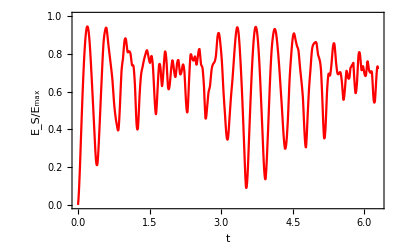

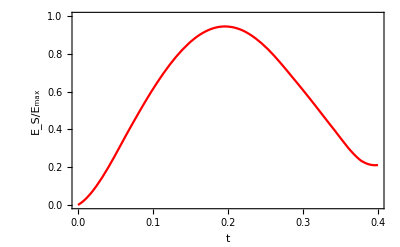

```mathematica
taumax=2*Pi;datafunc=Interpolation[datalist10];p2=Plot[datafunc[tau],{tau,0,taumax},Frame->True,PlotRange->{-0.000001,1},FrameLabel->{"t","E_S/E_max"},PlotStyle->Red];
Print[p2];
taumax=0.4;
p3=Plot[datafunc[tau],{tau,0,taumax},Frame->True,PlotRange->{-0.000001,1},FrameLabel->{"t","E_S/E_max"},PlotStyle->Red];
Print[p3];
```

```mathematica
zeros20={0.11803000000000001,0.35944000000000004,0.6124,0.8796100000000001,1.1420700000000001,1.4031600000000002,1.6959400000000002,2.00491,2.2899000000000003,2.54359,2.7854900000000002,3.0223600000000004,3.2634600000000002,3.51676,3.7800300000000004,4.035480000000001,4.283600000000001,4.5345,4.790520000000001,5.180750000000001,5.44373,5.68677,5.92515,6.167050000000001};
```

```mathematica
zeros10={0.19768000000000002,0.60299,1.03347,1.4758000000000002,1.9486900000000003,2.4637000000000002,2.9177000000000004,3.3271100000000002,3.72332,4.12781,4.550610000000001,4.9762900000000005,5.39733,5.863480000000001};
```

```mathematica
onezeros20=Table[{zeros20[[j]],0.98},{j,1,Length[zeros20]}];
```

```mathematica
onezeros10=Table[{zeros10[[j]],0.98},{j,1,Length[zeros10]}];
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->24},Frame->True,FrameStyle->Black];
```

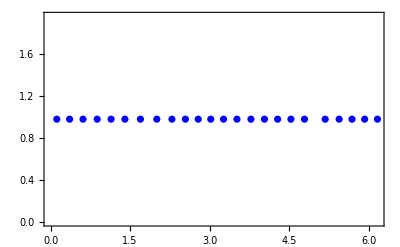

```mathematica
p4=ListPlot[onezeros20,PlotStyle->Blue]
```

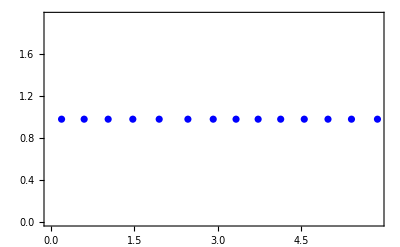

```mathematica
p4=ListPlot[onezeros10,PlotStyle->Blue]
```

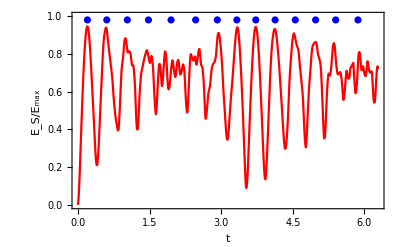

```mathematica
Show[p2,p4,PlotRange->{0,1}]
```

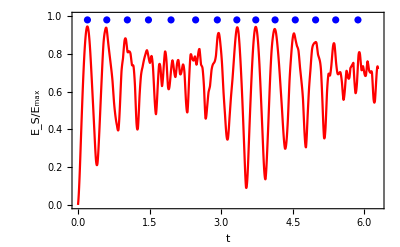

```mathematica
Show[p2,p4,PlotRange->{{0,2*Pi},{0,1}}]
```